```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/norbert/Dropbox (MIT)/StasPacking/Data/Thomson

Import the RC tree and some visualization data (colors):

```mathematica
GD=Import["../GD_Mathematica.mat"]//First//First;
MyColors=Import["../MyColors_Mathematica.mat"]//First;
RCAdj=Round[Import["../RCAdj.mat"][[1]]];
GRC=AdjacencyGraph[RCAdj];
RCa=GraphAutomorphismGroup[GRC];
NAutRC=GroupOrder[RCa];
RCDegrees = VertexDegree[GRC];
```

```mathematica
GRC
```

This is the IGraph package - only do this once:

```mathematica
PacletInstall["/Users/norbert/Downloads/IGraphM-0.3.90.paclet"]
```

Paclet[IGraphM,0.3.90,<>]

Load the package:

```mathematica
<<IGraphM`
```

IGraph/M 0.3.90 (April 28, 2017)

Evaluate IGDocumentation[] to get started.

```mathematica
IGDocumentation[]
```

## Subisos for T0 Thomson graph

Obtain the T0 Thomson graph graph and Vertex coordinates.

```mathematica
TADJ=Import["ADJ_Thomson11.mat"]//First;
TV = Import["Thomson11.mat"];
T0Coords=TV[[3]];
T0G=AdjacencyGraph[Round[TADJ]];
a1=GraphAutomorphismGroup[T0G];
NAutThomson=GroupOrder[a1];
```

There are 62k sub-isomorphisms with which the RC tree can be “embedded” within the T0 graph:

```mathematica
IGVF2SubisomorphismCount[GRC,T0G]
```

62256

Find all possibilities explicitly:

```mathematica
AllSubisos = IGVF2FindSubisomorphisms[GRC,T0G];
```

```mathematica
AllCoords=Table[0,{i,1,Length[AllSubisos]}];
AllAdjs=Table[0,{i,1,Length[AllSubisos]}];
For[m=1,m≤Length[AllSubisos], m++,
map=AllSubisos[[m]];
inv=Apply[Normal,GroupBy[Normal[map],Last->First],1];
AllAdjs[[m]]=AdjacencyMatrix[T0G][[Values[map],Values[map]]];
(* Don't need to project on unit sphere because already so by construction *)
AllCoords[[m]]=T0Coords[[Values[map]]];
];
```

```mathematica
Export["T0SubisoCoords.mat",AllCoords];
Export["T0SubisoAdjs.mat",AllAdjs];
```

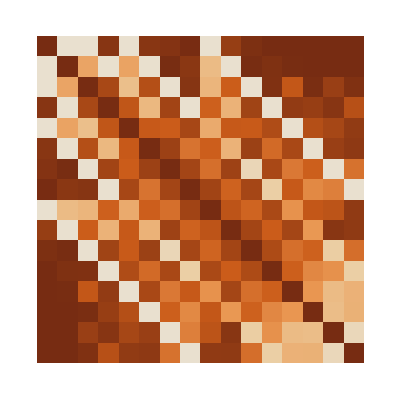

```mathematica
ArrayPlot[Total[AllAdj]/Length[AllSubisos],ColorFunction->"SiennaTones"]
```

## Subisos for T1 Thomson graph

Now repeat everything for the T01 Thomson graph:

```mathematica
TADJ=Import["ADJ_Thomson2.mat"]//First;
TV = Import["Thomson2.mat"];
T1Coords=TV[[3]];
T1G=AdjacencyGraph[Round[TADJ]];
a1=GraphAutomorphismGroup[T1G];
NAutThomson=GroupOrder[a1];
```

There are 94k sub-isomorphisms with which the RC tree can be “embedded” within the T1 graph:

```mathematica
IGVF2SubisomorphismCount[GRC,T1G]
```

94344

Find all possibilities explicitly:

```mathematica
AllSubisos = IGVF2FindSubisomorphisms[GRC,T1G];
```

```mathematica
AllCoords=Table[0,{i,1,Length[AllSubisos]}];
AllAdjs=Table[0,{i,1,Length[AllSubisos]}];
For[m=1,m≤Length[AllSubisos], m++,
map=AllSubisos[[m]];
inv=Apply[Normal,GroupBy[Normal[map],Last->First],1];
AllAdjs[[m]]=AdjacencyMatrix[T1G][[Values[map],Values[map]]];
(* Don't need to project on unit sphere because already so by construction *)
AllCoords[[m]]=T1Coords[[Values[map]]];
];
```

```mathematica
Export["T1SubisoCoords.mat",AllCoords];
Export["T1SubisoAdjs.mat",AllAdjs];
```

Debugging routines down here:

```mathematica
VertexReplace[GRC,Normal[map]]
```

```mathematica
m=1000;
map=AllSubisos[[m]];
inv=Apply[Normal,GroupBy[Normal[map],Last->First],1];
NewAdj=AdjacencyMatrix[T0G][[Values[map],Values[map]]];
NewCoords=T0Coords[[Values[map]]];
```

```mathematica
NewG=AdjacencyGraph[NewAdj];
CoordRule=Table[i->NewCoords[[i]],{i,1,16}];
```

```mathematica
GraphPlot3D[NewG,VertexCoordinateRules->CoordRule,VertexLabeling->True,VertexRenderingFunction->({RGBColor[MyColors[[GD[[#2]]+1]]],Sphere[#1,.2]}&),Lighting->"Neutral"]
```

-Graphics3D-